# Cosmomathica v1.0

Santiago Casas, 2018

This notebook demonstrates how to use the Cosmomathica package version 1.0

## Calling external programs

### Initialization

First, load the Cosmomathica package

```mathematica
NotebookDirectory[]
```

/local/home/scasas/CosmoProjects/cosmomathica/

```mathematica
<<(NotebookDirectory[]<>"cosmomathica.m")
```

### Transfer

```mathematica
?Transfer
```

Transfer[OmegaM, fBaryon, Tcmb, h] provides an interface to Eisenstein & Hu's fitting formula for the transfer function (high baryon case). It takes the total matter density Ω_M, the fraction of baryons Ω_b/Ω_M, the CMB temperature and the dimensionless Hubble constant h as input, and returns the sound horizon, the wavenumber k_peak where the spectrum has a maximum, the transfer function for CDM, baryons, both, or with no baryons or no wiggles.

This is how you call Eisenstein&Hu’s Transfer function code

```mathematica
tfdata=Transfer[0.25,0.35,2.7,0.67];
```

To see what kind of data has been returned, type this

```mathematica
tfdata[[All,1]]
```

{Transfer[soundhorizon],Transfer[peak],Transfer[kvalues],Transfer[full],Transfer[baryon],Transfer[cdm],Transfer[nowiggles],Transfer[zerobaryons]}

To access it, use the replacement rules, e.g. for the sound horizon

```mathematica
Transfer["soundhorizon"]/.tfdata
```

97.1983

or for the various transfer functions

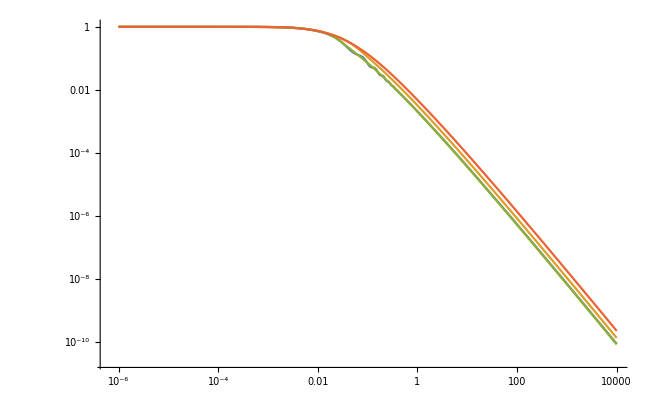

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose[{Transfer["kvalues"]/.tfdata,pk}],{pk,{
Transfer["full"],
Transfer["cdm"],
Transfer["nowiggles"],
Transfer["zerobaryons"]
}/.tfdata}],Joined->True]
```

```mathematica
?TFPower
```

TFPower[OmegaM, OmegaB, OmegaMN, DegenNu, OmegaL, h, z] provides an interface to Eisenstein & Hu's fitting formula for the transfer function (mixed matter case). It takes the total matter density Ω_M, the baryon density Ω_b, the massive neutrino density Ω_ν, the integer number of degenerate massive neutrino species, the dark energy density Ω_L, the dimensionless Hubble constant h, and the redshift z as input, and return the transfer function at the given redshift.

The mixed matter case is a bit simpler :

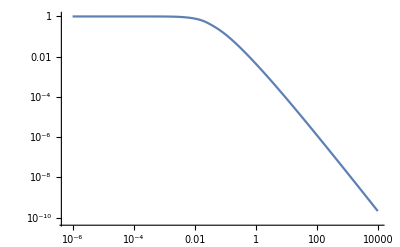

```mathematica
ListLogLogPlot[TFPower[0.3,0.05,0,0,0.7,0.7,0.8],Joined->True]
```

### Halofit

```mathematica
?Halofit
```

Halofit[OmegaM, OmegaL, gammaShape, sigma8, ns, betaP, z0] provides an interface to the halofit algorithm by Robert E. Smith et al. (reimplemented in C by Martin Kilbinger). It takes the total matter density Ω_M, the vacuum energy density Ω_L, a shape factor, σ_8, n_s, β_p, and a fixed redshift z_0 as input, and returns the nonlinear matter power spectrum (computed in three ways: linearly with the BBKS alogorithm, nonlinear with the algorithm by Peacock and Dobbs, or nonlinearly with the Halofit algorithm) at 20 different values of the scale factor and the convergence power spectrum in tabulated form.

Call the Halofit+ code

```mathematica
hfdata=Halofit[0.30,0.70,0.259,0.79,0.96,1.0,1.0];
```

View the output data options

```mathematica
hfdata[[All,1]]
```

{Halofit[avalues],Halofit[kvalues],Halofit[ellvalues],Halofit[kappaBBKS],Halofit[BBKS],Halofit[kappaPD96],Halofit[PD96],Halofit[kappaHalofit],Halofit[Halofit]}

Plot the matter power spectrum using the Halofit algorithm at different redshifts

```mathematica
halofitkvalues=Halofit["kvalues"]/.hfdata
```

{0.0001,0.000125893,0.000158489,0.000199526,0.000251189,0.000316228,0.000398107,0.000501187,0.000630957,0.000794328,0.001,0.00125893,0.00158489,0.00199526,0.00251189,0.00316228,0.00398107,0.00501187,0.00630957,0.00794328,0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.,125.893,158.489,199.526,251.189,316.228,398.107,501.187,630.957,794.328,1000.,1258.93,1584.89,1995.26,2511.89,3162.28,3981.07,5011.87,6309.57,7943.28,10000.}

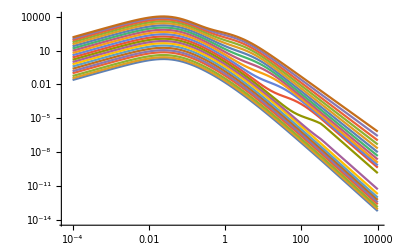

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose[{halofitkvalues,pk}],
{pk,Halofit["Halofit"]/.hfdata}],
Joined->True]
```

```mathematica
halofitpkz0=(Table[Transpose[{halofitkvalues,pk}],{pk,Halofit["Halofit"]/.hfdata}])[[-1]];
```

Note that Halofit[“Halofit”] returns a list of lists, each of which corresponds to the power spectrum at a different redshift or scale factor. The scale factors are as follows

```mathematica
Halofit["avalues"]/.hfdata
```

{0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.}

Plot the convergence power spectrum using three different algorithms

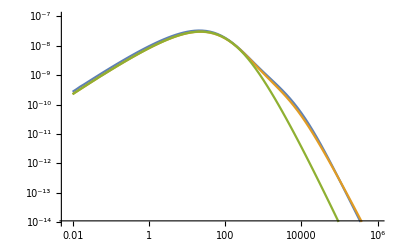

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose[{Halofit["ellvalues"]/.hfdata,kappa}],{kappa,{
Halofit["kappaHalofit"],
Halofit["kappaPD96"],
Halofit["kappaBBKS"]
}/.hfdata}],Joined->True,PlotRange->{1*^-14,1*^-7}]
```

### FrankenEmu

```mathematica
?FrankenEmu
```

FrankenEmu[omegaM, omegaB, h, sigma8, ns, w] provides an interface to FrankenEmu by Earl Lawrence. It takes ω_M, ω_b, h, σ_8, n_s, and the equation of state w, and returns the nonlinear matter power spectrum at five different redshifts as well as z, H, d (all at last scattering), and the sound horizon. The Hubble parameter h can also be omitted, in which case it will be determined from the CMB just as in CosmicEmu. Additional cosmological parameters are only returned if h is missing.

Call FrankenEmu

```mathematica
fedata=FrankenEmu[0.3*0.67^2,0.05*0.67^2,0.67,0.79,0.96,-1];
```

View the output

```mathematica
fedata[[All,1]]
```

{FrankenEmu[zvalues],FrankenEmu[pk]}

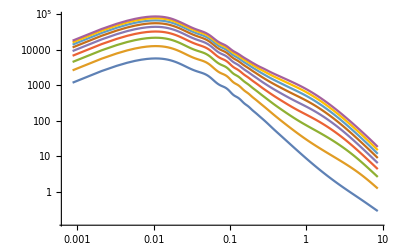

```mathematica
ListLogLogPlot[Evaluate@Table[pk,{pk,FrankenEmu["pk"]/.fedata}],Joined->True]
```

```mathematica
frankenemupkz0=(Table[pk,{pk,FrankenEmu["pk"]/.fedata}])[[-1]];
```

Convert FrankenEmu units from [k]=1/Mpc to h/Mpc:

```mathematica
frankenemupkz0= Transpose[{frankenemupkz0[[All,1]]/0.67,(0.67^3)* frankenemupkz0[[All,2]]}];
```

```mathematica
Interrupt[]
```

$Aborted

### CAMB

CAMB takes a lot of parameters. In Cosmomathica, most of them are being treated as options with default values while some of them are regular parameters that have to be specified. The distinction is arbitrary. These are the default options (see the CAMB documentation for details):

```mathematica
?CAMB
```

CAMB[OmegaC, OmegaB, h] :
provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes a few parameters as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.

```mathematica
Options[CAMB]
```

{MGflag→0,pureMGflag→1,altMGflag→1,QSAflag→1,mugammapar→2,musigmapar→1,QRpar→1,DEmodel→1,GRtrans→0.001,B1→0.,lambda12→0.,B2→0.,lambda22→0.,ss→4.,E11→0.,E22→0.,mu0→-1.,sigma0→0.,MGQfix→0.,MGRfix→0.,Qnot→1.,Rnot→1.,sss→0.,Lindergamma→0.545,betastar→0.,astar→0.5,xistar→0.001,beta0→1.,xi0→0.0001,DilS→0.24,DilR→1.,FR0→0.0001,FRn→1.,w0ppf→-1.,wappf→0.,Tcmb→2.7255,OmegaNu→0,OmegaK0→0.,YHe→0.24,MasslessNeutrinos→3.046,MassiveNeutrinos→0,NuMassDegeneracies→{0},NuMassFractions→{1},ScalarInitialCondition→adiabatic,NonLinear→pk,HalofitVersion→4,WantCMB→True,WantTransfer→True,WantCls→False,WantScalars→False,WantVectors→False,WantTensors→False,ScalarSpectralIndex→{0.96},ScalarRunning→{0},TensorSpectralIndex→{0},RatioScalarTensorAmplitudes→{1},ScalarPowerAmplitude→{2.1×10^-9},PivotScalar→0.05,PivotTensor→0.05,DoReionization→True,UseOpticalDepth→False,OpticalDepth→0.,ReionizationRedshift→10.,ReionizationFraction→1.,ReionizationDeltaRedshift→0.5,AccuracyBoost→2,TransferHighPrecision→True,TransferInterpMatterPower→False,WantZstar→True,WantZdrag→True,OutputNormalization→1,MaxEll→1500,MaxEtaK→4000.,MaxEtaKTensor→800.,MaxEllTensor→400,TransferKmax→5,TransferKperLogInt→50,TransferRedshifts→{0.},AccuratePolarization→True,AccurateReionization→False,AccurateBB→False,DoLensing→False,OnlyTransfers→False,DerivedParameters→True,MassiveNuMethod→best,debugIntFloats→False}

```mathematica
?MGflag
```

An option for CAMB/MGCAMB: 
          MG_flag = 0 :  default GR
          MG_flag = 1 :  pure MG models
          MG_flag = 2 :  alternative MG models
          MG_flag = 3 :  QSA models

```mathematica
?QSAflag
```

An option for CAMB/MGCAMB: 
QSA_flag = 1 : f(R)
QSA_flag = 2 : Symmetron      
QSA_flag = 3 : Dilaton
QSA_flag = 4 : Hu-Sawicki f(R)

```mathematica
?FR0
```

Parameter options for MGCAMB

```mathematica
?MasslessNeutrinos
```

An option for CAMB

```mathematica
?HalofitVersion
```

An option for CAMB. Integer number that chooses the Halofit version used in the non-linear matter power spectrum.
1: Original, 2: Bird, 3: Peacock, 4: Takahashi, 5: Mead, 6: Halo model, 7: Casarini,
8: Mead2015, 9: Winther-f(R)

Default values of some CAMB default options:

```mathematica
OptionValue[CAMB,#]&/@{MGflag,FR0,FRn, OmegaNu,MasslessNeutrinos,NuMassDegeneracies,NuMassFractions,ScalarSpectralIndex,ScalarPowerAmplitude,MaxEtaK,TransferKmax, HalofitVersion}
```

{0,0.0001,1.,0,3.046,{0},{1},{0.96},{2.1×10^-9},4000.,5,4}

Run the CAMB code (without lensing the scalar angular power spectrum will contain only three curves corresponding to C_TT, C_EE, C_TE - see the CAMB documentation for further information) with the transfer function for two different redshifts

```mathematica
cambdataLCDM=CAMB[0.25,0.05,0.67,TransferRedshifts->{1.5,0.}, WantCls->True,WantScalars->True, HalofitVersion->4];
```

```mathematica
cambdata4NoWin=CAMB[0.25,0.05,0.67,TransferRedshifts->{1.5,0.}, WantCls->True,WantScalars->True, MGflag->3, QSAflag->4, FR0->10^(-4), FRn->1, HalofitVersion->4];
```

```mathematica
(*cambdata4HaloWin=CAMB[0.25,0.05,0.67,TransferRedshifts->{1.5,0.}, WantCls->True,WantScalars->True, MGflag->3, QSAflag->4, FR0->10^(-4), FRn->1, HalofitVersion->9];*)
```

```mathematica
cambdata6NoWin=CAMB[0.25,0.05,0.67,TransferRedshifts->{1.5,0.}, WantCls->True,WantScalars->True, MGflag->3, QSAflag->4, FR0->10^(-6), FRn->1, HalofitVersion->4];
```

```mathematica
(*cambdata6HaloWin=CAMB[0.25,0.05,0.67,TransferRedshifts->{1.5,0.}, WantCls->True,WantScalars->True, MGflag->3, QSAflag->4, FR0->10^(-6), FRn->1, HalofitVersion->9];*)
```

```mathematica
cambdataLCDM[[All,1]]
```

{CAMB[age],CAMB[zstar],CAMB[rstar],CAMB[100thetastar],CAMB[zdrag],CAMB[rdrag],CAMB[kD],CAMB[100thetaD],CAMB[zEQ],CAMB[100thetaEQ],CAMB[sigma8],CAMB[CLscalar],CAMB[redshifts],CAMB[PSlinear],CAMB[PSnonlinear],CAMB[Transfer]}

Age of the universe:

```mathematica
CAMB["age"]/.cambdataLCDM
```

14.0639

```mathematica
CAMB["age"]/.cambdata4NoWin
```

14.0639

There is a σ_8 for each redshift and for each spectral index

```mathematica
CAMB["redshifts"]/.cambdataLCDM
```

{1.5,0.}

```mathematica
CAMB["sigma8"]/.cambdataLCDM
```

{{0.393337},{0.785823}}

```mathematica
CAMB["sigma8"]/.cambdata4NoWin
```

{{0.421716},{1.43167}}

Plot the scalar angular power spectrum for TT

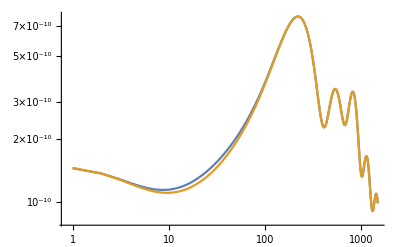

```mathematica
ListLogLogPlot[{(CAMB["CLscalar"]/.cambdata4NoWin)[[1]],(CAMB["CLscalar"]/.cambdataLCDM)[[1]]} ,Joined->True]
```

Plot the scalar angular power spectrum for EE and TE

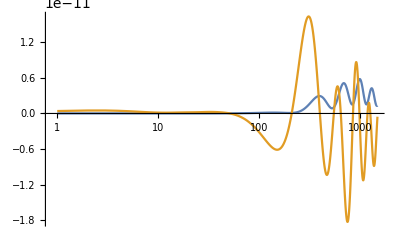

```mathematica
ListLogLinearPlot[(CAMB["CLscalar"]/.cambdataLCDM)[[2;;3]],Joined->True]
```

The results for the linear/nonlinear power spectrum as well as the transfer function contain a list for each redshift. Each one of those is a list of number pairs {k_i,P(k_i)} in the case of the power spectrum, and a list of seven numbers {k_i,T_1(k_i),..., T_6(k_i)} in case of the transfer function, each of which correspond to CDM, baryon, photon, massless neutrino, massive neutrinos, and total (massive).

Plot the nonlinear matter power spectrum for all redshifts

```mathematica
CAMB["redshifts"]/.cambdata4NoWin
```

{1.5,0.}

```mathematica
CAMB["redshifts"]/.cambdataLCDM
```

{1.5,0.}

```mathematica
redz=2;
```

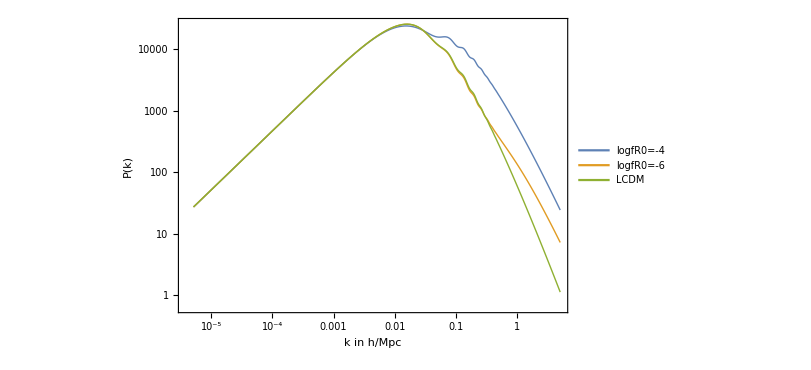

```mathematica
ListLogLogPlot[{((CAMB["PSlinear"]/.cambdata4NoWin)[[redz]]),((CAMB["PSlinear"]/.cambdata6NoWin)[[redz]]), ((CAMB["PSlinear"]/.cambdataLCDM)[[redz]])},Joined->True, PlotLegends->Placed[LineLegend[{"logfR0=-4","logfR0=-6", "LCDM"}], Scaled[{0.2,0.8}]], PlotStyle->Thick, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16](*Epilog->Inset[raplo, Scaled[{0.5,0.3}]]*)]
```

```mathematica
ratio4=Thread[{((CAMB["PSnonlinear"]/.cambdata4NoWin)[[redz]])[[All,1]], ((CAMB["PSnonlinear"]/.cambdata4NoWin)[[redz]])[[All,2]]/(((CAMB["PSnonlinear"]/.cambdataLCDM)[[redz]])[[All,2]])}];
(*ratio5=Thread[{((CAMB["PSlinear"]/.cambdata5)[[1]])[[All,1]], ((CAMB["PSlinear"]/.cambdata5)[[1]])[[All,2]]/(((CAMB["PSlinear"]/.cambdataLCDM)[[1]])[[All,2]])}];*)
ratio6=Thread[{((CAMB["PSnonlinear"]/.cambdata6NoWin)[[redz]])[[All,1]], ((CAMB["PSnonlinear"]/.cambdata6NoWin)[[redz]])[[All,2]]/(((CAMB["PSnonlinear"]/.cambdataLCDM)[[redz]])[[All,2]])}];
ratio1=Thread[{((CAMB["PSnonlinear"]/.cambdataLCDM)[[redz]])[[All,1]], ((CAMB["PSnonlinear"]/.cambdataLCDM)[[redz]])[[All,2]]/(((CAMB["PSnonlinear"]/.cambdataLCDM)[[redz]])[[All,2]])}];
```

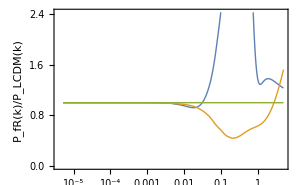

```mathematica
raplo=ListLogLinearPlot[{ratio4,  ratio6, ratio1},Joined->True (*PlotLegends->Placed[LineLegend[{"logfR0=-4,","logfR0=-5", "logfR0=-6", "LCDM"}], Scaled[{0.1,0.8}]]*), PlotStyle->Thick, Frame->True, FrameLabel->{"", Style["P_fR(k)/P_LCDM(k)", Bold, 10]} , ImageSize->{300,150}, FrameTicksStyle->Directive[Black,10]]
```

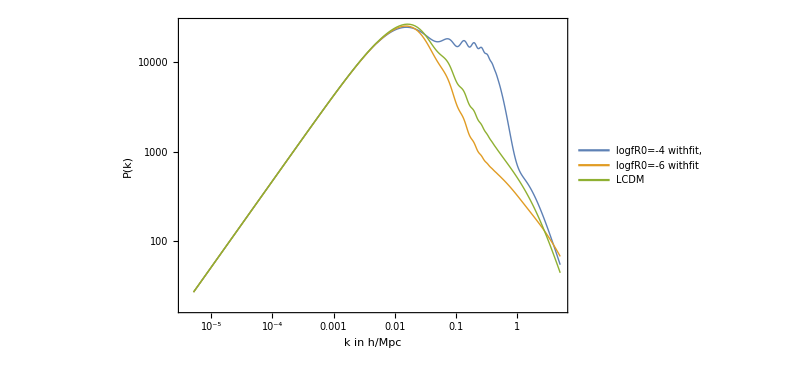

```mathematica
ListLogLogPlot[{((CAMB["PSnonlinear"]/.cambdata4NoWin)[[redz]]),((CAMB["PSnonlinear"]/.cambdata6NoWin)[[redz]]),(*((CAMB["PSlinear"]/.cambdata6NoWin)[[1]]),((CAMB["PSlinear"]/.cambdata6HaloWin)[[1]]),*) ((CAMB["PSnonlinear"]/.cambdataLCDM)[[redz]])},Joined->True, PlotLegends->Placed[LineLegend[{"logfR0=-4 withfit,","logfR0=-6 withfit", (*"logfR0=-6","logfR0=-6",*) "LCDM"}], Scaled[{0.2,0.8}]], PlotStyle->Thick, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplo, Scaled[{0.5,0.3}]]]
```

```mathematica
cambpkz0=(CAMB["PSnonlinear"]/.cambdata)[[-1]];
```

Plot the CDM and the Photon transfer function at the first redshift

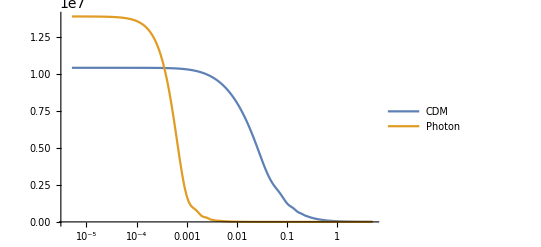

```mathematica
ListLogLinearPlot[{(CAMB["Transfer"]/.cambdata)[[1,All,{1,2}]], (CAMB["Transfer"]/.cambdata)[[1,All,{1,4}]]},Joined->True, PlotLegends->{"CDM", "Photon"}]
```

## Class (*Currently with a bug, ignore for now*)

```mathematica
(*?Class*)
```

Every parameter is configured by options. We build a .ini file from them and pass it on to Class. So every option of the form “key”->”value” becomes one line in the .ini file of the form “key = value”. Note that all values need to be strings. For details, read the file explanatory.ini which comes with the Class package.

```mathematica
(*classdata=Class["h" -> ".67","Omega_k"->"0.","n_s"->".9", "Omega_b"->"0.05",
"output"->"mTk,mPk",
"z_pk"->"0,1,2",
"gauge"->"synchronous"(*"newton"*),
"non linear"->"halofit",
"P_k_max_h/Mpc"->"10",
"modes"->"s",
"format"->"camb"];*)
```

View the output

```mathematica
(*classdata[[All,1]]*)
```

```mathematica
(*Class["sigma8"]/.classdata*)
```

Plot the linear power spectrum

```mathematica
(*ListLogLogPlot[Evaluate@Table[Transpose@{Class["kvalues"]/.classdata,(Class["PSlinear"]/.classdata)[[i]]},{i,{1,5,10}}],Joined->True]*)
```

Plot the non-linear power spectrum

```mathematica
(*ListLogLogPlot[Evaluate@Table[Transpose@{Class["kvalues"]/.classdata,(Class["PSnonlinear"]/.classdata)[[i]]},{i,{1,5,10}}],Joined->True]*)
```

## Compare Codes

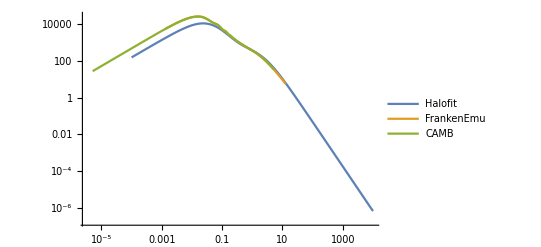

```mathematica
ListLogLogPlot[{halofitpkz0,frankenemupkz0, cambpkz0}, Joined->True, PlotLegends->{"Halofit", "FrankenEmu", "CAMB"}]
```

```mathematica
SetOptions[Interpolation, InterpolationOrder->1]
```

{InterpolationOrder→1,Method→Automatic,PeriodicInterpolation→False}

```mathematica
interphalofitpkz0=Interpolation[halofitpkz0]
interpfrankenemupkz0=Interpolation[frankenemupkz0]
interpcambpkz0=Interpolation[cambpkz0]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

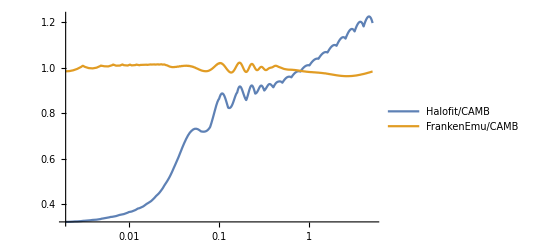

```mathematica
LogLinearPlot[{interphalofitpkz0[kk]/interpcambpkz0[kk],interpfrankenemupkz0[kk]/interpcambpkz0[kk]}, {kk,0.002,5},PlotLegends->{"Halofit/CAMB", "FrankenEmu/CAMB"}]
```